# Guard extraction over control flow — Findings (v0)

## gtpyhop-diagnostics, commit dc3f852: an if is a guard only if every successful path passes it

type: findings
topic: diagnostics_guard_cf
date: 2026-11-16
version: v0
prior-version: none (continues diagnostics_guard_nnf round 00, R6)
key-metric: unsound atoms over every action body of ≤ 6 statements: 0 (prior: 13,890 with the ast.walk reading)
decision-required: confirm

## Headline Result

metric:    unsound atoms extracted, every action body of ≤ 6 statements (if/else, loop, return state, return False, effect) over 3 tests
value:     0  (path-aware, dc3f852)
unit:      atoms
prior:     13,890 (ast.walk reading, 0.1.1)
direction: down

decision-required is confirm: file the control-flow issue together with dc3f852. The fix only removes atoms (R3, last column), the removal is proved sound for every program (R2), and the Python code computes exactly what the model proves (R5). Its cost is precision in two places: inside loops, and where the same test is read twice on a path (R4).

## Model

Round 00 proved that each guard's requirement splits into atoms soundly. This round asks which ifs have a requirement at all. explain_dead_end only analyses actions the planner recorded as not applicable (they returned False or None), so an atom is honest exactly when every other outcome implies it: success ⟹ atom. 0.1.1 found guards with ast.walk and read every if as guarding the whole action. dc3f852 walks the statements backwards and keeps, as (if, polarity) pairs, the requirements every successful path passes. The reading of each if is unchanged; its atoms are kept only if that pair is in the set.

statement | may succeed | required on every success | why
return state (any non-falsey return) | yes | nothing | succeeds here, whatever came before
return False / return None / return / raise | no | — | cannot succeed
if t: A else: B, A cannot succeed | as B | not t, plus what B needs | every success goes through B
if t: A else: B, B cannot succeed | as A | t, plus what A needs | every success goes through A
if t: A else: B, both can | yes | what both A and B need | a success may take either branch
loop, with, try: no success return inside | as what follows | what follows needs | every success leaves it and continues
loop, with, try: a success return inside | yes | nothing | a success may end inside it
anything else | as what follows | what follows needs | falls through
end of the function | no | — | falls off: returns None

Model syntax, inert so nothing simplifies before the rules see it: ok (return state), bail (return False, covering None, bare return and raise), eff (an effect), if[id, t, A, B], loop[id, A]. Tests are read on the state the action was called on, which is what explain_dead_end evaluates atoms against. A loop body runs on a fresh unknown c[id]: zero iterations, or at least one, which with tests read on the pre-state behaves as one.

## Results Tables

### R1. The root cause, on the shapes of the issue

```mathematica
With[{shapes={{"if a: if b: return False",{if[1,p,{if[2,q,{bail},{}]},{}],ok}},{"if a: ...return s;  if b: ...return s",{if[1,p,{eff,ok},{}],if[2,q,{eff,ok},{}]}},{"if a: return s;  if b: return False;  return s",{if[1,p,{ok},{}],if[2,q,{bail},{}],ok}},{"for o in objs: if b: return False",{loop[1,{if[2,q,{bail},{}]}],ok}},{"if a: return False  elif b: return False",{if[1,p,{bail},{if[2,q,{bail},{}]}],ok}},{"if a: if b: return s",{if[1,p,{if[2,q,{ok},{}]},{}]}}}},tbl[{"shape","success condition","ast.walk (0.1.1)","path-aware (dc3f852)"},({#1⟦1⟧,ToString[BooleanMinimize[sem[#1⟦2⟧,False]],InputForm],colour[#1⟦2⟧,oldReq[#1⟦2⟧]],showReq[#1⟦2⟧,newReq[#1⟦2⟧]]}&)/@shapes]]
```

shape | success condition | ast.walk (0.1.1) | path-aware (dc3f852)
if a: if b: return False |  !p ||  !q |  !q | 
if a: ...return s;  if b: ...return s | p || q | p,  q | 
if a: return s;  if b: return False;  return s | p ||  !q | p,   !q | 
for o in objs: if b: return False |  !q ||  !c[1] |  !q | 
if a: return False  elif b: return False |  !p &&  !q |  !q,   !p |  !p,   !q
if a: if b: return s | p && q | q,  p | p,  q

Red marks an atom the success condition does not imply. The first four shapes lose their atoms; the last two, which have a single path to success, keep every one.

### R2. Proof for every program, by induction on the statement list

Invariant Inv(f, {mayOk, R}) for a block whose success condition is f: f implies every literal in R, and if mayOk is False then f is unsatisfiable. The analysis computes a block's result from its first statement and the result for the rest, so it suffices that each clause preserves Inv, given Inv for the children (IH). R is a set, and f ⟹ And(R) holds literal by literal, so one representative literal per set is enough: x common to both branches, ra and rb in one only, rk from the continuation.

```mathematica
tbl[{"clause","obligation","result"},{{"return state","sem = True, result {True, {}}",mark[T[inv[True,True,{}],{}]]},{"return False / raise","sem = False, result {False, {}}",mark[T[inv[False,False,{}],{}]]},{"effect, anything that falls through","sem = k, result = K",mark[T[inv[k,okK,{rk}]⇒inv[k,okK,{rk}],{k,okK,rk}]]},{"if, both branches cannot succeed","result {False, {}}",mark[T[inv[a,False,{ra}]&&inv[b,False,{rb}]⇒inv[(t&&a)||(!t&&b),False,{}],{t,a,b,ra,rb}]]},{"if, body cannot succeed","result {True, R_B ∪ {!t}}",mark[T[inv[a,False,{ra}]&&inv[b,True,{rb}]⇒inv[(t&&a)||(!t&&b),True,{rb,!t}],{t,a,b,ra,rb}]]},{"if, else cannot succeed","result {True, R_A ∪ {t}}",mark[T[inv[a,True,{ra}]&&inv[b,False,{rb}]⇒inv[(t&&a)||(!t&&b),True,{ra,t}],{t,a,b,ra,rb}]]},{"if, both may succeed","result {True, R_A ∩ R_B}",mark[T[inv[a,True,{x,ra}]&&inv[b,True,{x,rb}]⇒inv[(t&&a)||(!t&&b),True,{x}],{t,a,b,x,ra,rb}]]},{"compound with a success return inside","result {True, {}}",mark[T[inv[(cc&&a)||(!cc&&k),True,{}],{cc,a,k}]]},{"compound without one","result = K, by the lemma a ⟹ k",mark[T[(a⇒k)&&inv[k,okK,{rk}]⇒inv[(cc&&a)||(!cc&&k),okK,{rk}],{cc,a,k,okK,rk}]]},{"lemma: no success return ⟹ a ⟹ k","bail, fall-through, if and loop (IH on the parts)",mark[T[(False⇒k)&&(k⇒k)&&((a⇒k)&&(b⇒k)⇒((t&&a)||(!t&&b)⇒k))&&((a⇒k)⇒((cc&&a)||(!cc&&k)⇒k)),{t,a,b,cc,k}]]},{"end of the function","K0 = {False, {}} for k = False",mark[T[inv[False,False,{}],{}]]},{"filter, then split","kept ⊆ R, and round 00 R2: requirement ⟹ each atom",mark[T[(s⇒l)&&(l⇒at)⇒(s⇒at),{s,l,at}]]}}]
```

clause | obligation | result
return state | sem = True, result {True, {}} | proved
return False / raise | sem = False, result {False, {}} | proved
effect, anything that falls through | sem = k, result = K | proved
if, both branches cannot succeed | result {False, {}} | proved
if, body cannot succeed | result {True, R_B ∪ {!t}} | proved
if, else cannot succeed | result {True, R_A ∪ {t}} | proved
if, both may succeed | result {True, R_A ∩ R_B} | proved
compound with a success return inside | result {True, {}} | proved
compound without one | result = K, by the lemma a ⟹ k | proved
lemma: no success return ⟹ a ⟹ k | bail, fall-through, if and loop (IH on the parts) | proved
end of the function | K0 = {False, {}} for k = False | proved
filter, then split | kept ⊆ R, and round 00 R2: requirement ⟹ each atom | proved

with and try are read as the compound rows: a success either returns inside them (nothing required) or leaves them and continues (the lemma: without a success return inside, every success goes through what follows, whatever path the body took or wherever it was cut short). Nested function definitions are not entered, so their returns are not the action's.

### R3. Exhaustive cross-check

```mathematica
Length[progs]
```

94350

```mathematica
With[{rows=Table[Prepend[Total[checkProg/@number/@blocks[n]],n],{n,1,6}]},tbl[{"size","programs","walk","unsound","path","unsound","R unsound","no-ok wrong","added"},Append[rows,Prepend[Total[rows⟦All,2;;All⟧],"all"]]]]
```

size | programs | walk | unsound | path | unsound | R unsound | no-ok wrong | added
1 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 15 | 3 | 0 | 0 | 0 | 0 | 0 | 0
3 | 114 | 39 | 3 | 9 | 0 | 0 | 0 | 0
4 | 969 | 450 | 60 | 114 | 0 | 0 | 0 | 0
5 | 8847 | 5175 | 936 | 1386 | 0 | 0 | 0 | 0
6 | 84402 | 59481 | 12891 | 16173 | 0 | 0 | 0 | 0
all | 94350 | 65148 | 13890 | 17682 | 0 | 0 | 0 | 0

Every action body of up to 6 statements (size) over three tests, each checked over every assignment of the tests and of each loop's run-or-not. walk and path: atoms from the ast.walk reading (0.1.1) and the path-aware one (dc3f852), each followed by how many of them the success condition does not imply, by truth table. R unsound: literals in the analysis' whole set R that are not implied. no-ok wrong: programs the analysis says cannot succeed but can. added: programs where the fix has an atom the old reading lacked.

### R4. Precision: what the fix gives up

A dropped atom is a loss only if it was sound and the action can succeed (in a program that never succeeds every atom is vacuously sound).

```mathematica
With[{lost=Join@@Function[P,If[satisfiable[P],({P,#1}&)/@necessary[P,Complement[oldReq[P],newReq[P]]],{}]]/@progs},With[{inside=Select[lost,inLoop[#1⟦1⟧,#1⟦2,1⟧]&],rep=Select[lost,!inLoop[#1⟦1⟧,#1⟦2,1⟧]&&repeats[#1⟦1⟧]&]},tbl[{"sound atoms the fix drops, in bodies that can succeed","count","smallest example","atom dropped"},{({"if inside a loop",Length[inside],showP[#1⟦1⟧],ToString[lit@@#1,InputForm]}&)[First[SortBy[inside,LeafCount]]],({"a test repeated on the path",Length[rep],showP[#1⟦1⟧],ToString[lit@@#1,InputForm]}&)[First[SortBy[rep,LeafCount]]],{"anything else",Length[lost]-Length[inside]-Length[rep],"—","—"},{"vacuous (the body never succeeds), for comparison",totals⟦2⟧-totals⟦3⟧-totals⟦4⟧-Length[lost],"",""}}]]]
```

sound atoms the fix drops, in bodies that can succeed | count | smallest example | atom dropped
if inside a loop | 2193 | {loop[{if[2, p, {bail}, {ok}]}]} |  !p
a test repeated on the path | 1326 | {if[p, {ok}, {if[2, p, {}, {bail}]}]} | p
anything else | 0 | — | —
vacuous (the body never succeeds), for comparison | 30057 |  |

Two causes, and only two. Inside a loop, the rule reads nothing: with for o in objs: if a: return s as the only success, the action needs the loop to run and a to hold, but the rule gives up both to stay sound when the loop runs zero times. In real domains such tests also read loop variables that no trace binds, so they could not have been evaluated. Where a test repeats, the rule treats each if as independent: in if a: return s else: (if a: pass else: return False), the second test of a is decided by the first, so a is necessary, but no if requires it on every path. Round 00 found its own precision gap in the same place, where a leaf repeats.

### R5. The code computes the model

The proof is about the model, so this checks that guards.py computes exactly what the model predicts, for both readings, on every program of R3. scripts/cf_agree.py renders each program as a Python action, runs extract_action_guards from 0.1.1 (dc3f852^) and from dc3f852, maps each atom back to its if, and compares.

```mathematica
Module[{json=FileNameJoin[{$TemporaryDirectory,"guard_cf_programs.json"}],old=FileNameJoin[{$TemporaryDirectory,"guard_cf_old_guards.py"}],new=FileNameJoin[{$TemporaryDirectory,"guard_cf_new_guards.py"}],res},Export[json,(Association["prog"->toJ[#1],"old"->oldReq[#1],"new"->newReq[#1]]&)/@progs,"RawJSON","Compact"->True];WriteString[old,RunProcess[{"git","-C",$repo,"show","dc3f852^:packages/gtpyhop-diagnostics/src/gtpyhop/diagnostics/guards.py"},"StandardOutput"]];Close[old];WriteString[new,RunProcess[{"git","-C",$repo,"show","dc3f852:packages/gtpyhop-diagnostics/src/gtpyhop/diagnostics/guards.py"},"StandardOutput"]];Close[new];res=RunProcess[{"python3","-S",FileNameJoin[{$here,"scripts","cf_agree.py"}],old,new,json}];DeleteFile[{json,old,new}];{res["ExitCode"],StringTrim[res["StandardOutput"]]}]
```

{0,programs=94350 old_mismatches=0 new_mismatches=0}

### R6. The bundled reproductions

rikyu_hpc a_submit_job, with p = launcher is not None, q = launcher != 'mpirun', r = processes_per_node < 1: if p: (if q: return False; if r: return False). A job with no launcher and processes_per_node = 0 (the documented "unset") that fails elsewhere:

```mathematica
With[{P={if[1,p,{if[2,q,{bail},{}],if[3,r,{bail},{}]},{}],ok},s={p->False,q->True,r->True}},tbl[{"reading","atoms","atoms that evaluate false"},{{"ast.walk (0.1.1)",showReq[P,oldReq[P]],showReq[P,Select[oldReq[P],!(lit[P,#1]/.s)&]]},{"path-aware (dc3f852)",showReq[P,newReq[P]],showReq[P,Select[newReq[P],!(lit[P,#1]/.s)&]]}}]]
```

reading | atoms | atoms that evaluate false
ast.walk (0.1.1) |  !q,   !r |  !q,   !r
path-aware (dc3f852) |  |

In the real action q reads the local launcher, which the evaluator cannot bind, so 0.1.1 lists it as unevaluated; r reads a parameter and is named as a blocker. bio_opentrons a_open_thermocycler_lid, with p = the lid is open: if p: return state (idempotent), then open it.

```mathematica
With[{P={if[1,p,{ok},{}],eff,ok}},tbl[{"reading","atoms","success condition","named when the lid is closed and another guard fails"},{{"ast.walk (0.1.1)",showReq[P,oldReq[P]],ToString[BooleanMinimize[sem[P,False]],InputForm],showReq[P,Select[oldReq[P],!(lit[P,#1]/.p->False)&]]},{"path-aware (dc3f852)",showReq[P,newReq[P]],ToString[BooleanMinimize[sem[P,False]],InputForm],showReq[P,Select[newReq[P],!(lit[P,#1]/.p->False)&]]}}]]
```

reading | atoms | success condition | named when the lid is closed and another guard fails
ast.walk (0.1.1) | p | True | p
path-aware (dc3f852) |  | True |

## Observations

Signal | Baseline / Expected | Observed [source] | Interpretation
unsound atoms | 0 for a correct extractor | 13,890 → 0 [R3] | the class is closed up to the bound, and for every program by R2
atoms added | 0: the fix only filters | 0 [R3] | no new or reworded atom can appear
model vs code | agree on every program | 0 mismatches, both readings [R5] | the proof is about the shipped guards.py
precision cost | small | every non-vacuous loss is inside a loop or on a repeated test [R4] | the price of reading nothing inside a loop, and of treating tests as independent
bundled examples | estimate: 11 actions, 13 atoms | 12 actions, 16 atoms; recognition 330 of 335 unchanged | the estimate missed early success returns and else branches
consumer corpus | estimate: 27 actions, 53 atoms | 50 actions, 105 atoms; recognition 5,808 → 5,807 | the lost action's only atom read a loop variable and was never evaluable

### Scope: what this does not prove

The bundled and corpus counts are measurements, made with diagnostics_guard_nnf/scripts/examples_diff.py and corpus.py and listed in the commit message, not computed here.

Tests are read on the state the action was called on. A guard that reads state the action has already changed is a separate, older limitation, untouched here.

The enumeration omits break, continue, while-else, with, try and match. R2 covers them through the compound rows; the property case in tools/diagnostics_guard_check.py executes generated bodies with loops and raise.

Diagnostics run after find_plan returns; none of this changes which plans are found.

## Charts & Visualizations

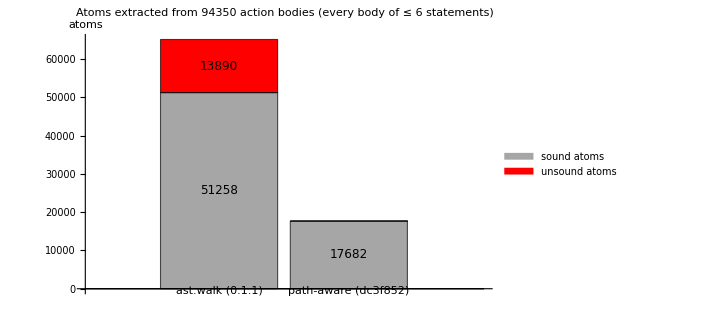

```mathematica
With[{d=Total[checkProg/@progs]},BarChart[{{d⟦2⟧-d⟦3⟧,d⟦3⟧},{d⟦4⟧,0}},ChartLayout->"Stacked",ChartLabels->{{"ast.walk (0.1.1)","path-aware (dc3f852)"},None},ChartLegends->Placed[{"sound atoms","unsound atoms"},Below],ChartStyle->{GrayLevel[0.65],Red},AxesLabel->{None,"atoms"},LabelingFunction->(If[#1>0,Placed[Style[#1,Black,12],Center],None]&),PlotLabel->"Atoms extracted from "<>TextString[d⟦1⟧]<>" action bodies (every body of ≤ 6 statements)",ImageSize->520]]
```

Caption: the ast.walk reading extracts unsound atoms (red) and the path-aware one none. The grey shrinks too, but most of the sound atoms it drops are vacuous, from bodies that can never succeed (R4).

## Contradictions & Surprises

Round 00 said a_submit_job's launcher != 'mpirun' is reported as failed. It is extracted, but it reads a local the evaluator cannot bind, so it lands as unevaluated. The false blocker that is actually named is its sibling processes_per_node < 1 (R6).

The upper-bound script undercounted. It missed bio_opentrons a_open_thermocycler_lid, whose idempotent early return state 0.1.1 read as requiring the lid already open, and the else branch of rikyu_hpc a_fs_tail.

## Steering Questions

[now] File the control-flow issue (ISSUE_DRAFT.md) with dc3f852 as its fix, then release as a patch?

[next run] Precision: conjoin a nested bail's enclosing test into one atom (if C: if T: return False → not (C and T)), and turn a loop bail into all(...) over the loop. Both add atoms, so both are features rather than fixes.

## Pointers

Commit dc3f852 (fix), on top of b0115ef (round 00 of diagnostics_guard_nnf)

tools/diagnostics_guard_check.py: 14 cases, including the executed control-flow property case, in checks.yml

scripts/cf_agree.py next to this notebook (R5); diagnostics_guard_nnf/scripts/ for the measurements

## Appendix: definitions (initialization cells)

Inert syntax ok, bail, eff, if[id, t, A, B], loop[id, A] over tests p, q, r. sem is the success condition, an mirrors guards._required_on_success, oldPol the per-if reading both versions share, oldReq the 0.1.1 result and newReq the dc3f852 result. The notebook has its own context (CellContext -> Notebook).

```mathematica
tests={p,q,r}
```

```mathematica
sem[{},k_]:=k
```

```mathematica
sem[{ok,___},k_]:=True
```

```mathematica
sem[{bail,___},k_]:=False
```

```mathematica
sem[{eff,rest___},k_]:=sem[{rest},k]
```

```mathematica
sem[{if[i_,t_,A_,B_],rest___},k_]:=With[{kk=sem[{rest},k]},(t&&sem[A,kk])||(!t&&sem[B,kk])]
```

```mathematica
sem[{loop[i_,A_],rest___},k_]:=With[{kk=sem[{rest},k]},(c[i]&&sem[A,kk])||(!c[i]&&kk)]
```

```mathematica
succIn[A_]:=!FreeQ[A,ok]
```

```mathematica
an[{},st_]:=st
```

```mathematica
an[{s_,rest___},st_]:=step[s,an[{rest},st]]
```

```mathematica
step[ok,_]:={True,{}}
```

```mathematica
step[bail,_]:={False,{}}
```

```mathematica
step[eff,st_]:=st
```

```mathematica
step[if[i_,t_,A_,B_],st_]:=Module[{a=an[A,st],b=an[B,st]},Which[!a⟦1⟧&&!b⟦1⟧,{False,{}},!a⟦1⟧,{True,b⟦2⟧∪{{i,True}}},!b⟦1⟧,{True,a⟦2⟧∪{{i,False}}},True,{True,a⟦2⟧∩b⟦2⟧}]]
```

```mathematica
step[loop[i_,A_],st_]:=If[succIn[A],{True,{}},st]
```

```mathematica
topBail[A_]:=MemberQ[A,bail]
```

```mathematica
oldPol[if[i_,t_,A_,B_]]:=Which[topBail[A],True,succIn[A],False,B=!={}&&topBail[B],False,True,None]
```

```mathematica
ifs[P_]:=Cases[P,_if,∞]
```

```mathematica
testOf[P_,i_]:=FirstCase[P,if[i,t_,__]:>t,Missing[],∞]
```

```mathematica
oldReq[P_]:=DeleteCases[({#1⟦1⟧,oldPol[#1]}&)/@ifs[P],{_,None}]
```

```mathematica
newReq[P_]:=oldReq[P]∩an[P,{False,{}}]⟦2⟧
```

```mathematica
lit[P_,{i_,neg_}]:=If[neg,!testOf[P,i],testOf[P,i]]
```

```mathematica
vars[P_]:=Join[tests,Cases[P,loop[i_,_]:>c[i],∞]]
```

```mathematica
stmts[1]={ok,bail,eff}
```

```mathematica
stmts[n_/;n≥2]:=stmts[n]=Join[Flatten[Table[Outer[sIf,tests,blocks[m],blocks[n-1-m],1],{m,0,n-2}],3],sLoop/@blocks[n-1]]
```

```mathematica
blocks[0]={{}}
```

```mathematica
blocks[n_/;n≥1]:=blocks[n]=Select[Flatten[Table[Outer[Prepend[#2,#1]&,stmts[m],blocks[n-m],1],{m,1,n}],2],FreeQ[Most[#1],ok|bail]&]
```

```mathematica
nb[l_List]:=nb/@l
```

```mathematica
nb[sIf[t_,A_,B_]]:=With[{i=++$id},if[i,t,nb[A],nb[B]]]
```

```mathematica
nb[sLoop[A_]]:=With[{i=++$id},loop[i,nb[A]]]
```

```mathematica
nb[s_]:=s
```

```mathematica
number[P_]:=Block[{$id=0},nb[P]]
```

```mathematica
tt[f_,v_]:=Boole[BooleanTable[f,v]]
```

```mathematica
necessary[P_,req_]:=With[{v=vars[P]},With[{S=tt[sem[P,False],v]},Select[req,Min[1-S+tt[lit[P,#1],v]]==1&]]]
```

```mathematica
checkProg[P_]:=checkProg[P]=Module[{st=an[P,{False,{}}],o=oldReq[P],n=newReq[P]},{1,Length[o],Length[o]-Length[necessary[P,o]],Length[n],Length[n]-Length[necessary[P,n]],Length[st⟦2⟧]-Length[necessary[P,st⟦2⟧]],Boole[!st⟦1⟧&&Max[tt[sem[P,False],vars[P]]]==1],Boole[!SubsetQ[o,n]]}]
```

```mathematica
satisfiable[P_]:=Max[tt[sem[P,False],vars[P]]]==1
```

```mathematica
inLoop[P_,i_]:=!FreeQ[Cases[P,loop[_,A_]:>A,∞],if[i,___]]
```

```mathematica
repeats[P_]:=!DuplicateFreeQ[Cases[P,if[_,t_,__]:>t,∞]]
```

```mathematica
T[f_,v_]:=TautologyQ[f,v]
```

```mathematica
inv[f_,okq_,R_]:=(f⇒And@@R)&&(!okq⇒!f)
```

```mathematica
showP[P_]:=ToString[P/.{if[i_,t_,A_,B_]:>if[t,A,B],loop[i_,A_]:>loop[A]},InputForm]
```

```mathematica
showReq[P_,req_]:=Row[Riffle[(ToString[lit[P,#1],InputForm]&)/@req,",  "]]
```

```mathematica
colour[P_,req_]:=Row[Riffle[(With[{s=ToString[lit[P,#1],InputForm]},If[necessary[P,{#1}]==={#1},s,Style[s,Red]]]&)/@req,",  "]]
```

```mathematica
tbl[headers_,rows_]:=Grid[Prepend[rows,(#1&)/@headers],Frame->All,Alignment->Left,Background->{None,{GrayLevel[0.9]}},Spacings->{1.2,0.6}]
```

```mathematica
mark[b_]:=If[TrueQ[b],Style["proved",Darker[Green]],Style["fails",Red]]
```

```mathematica
toJ[ok]="ok"
```

```mathematica
toJ[bail]="bail"
```

```mathematica
toJ[eff]="eff"
```

```mathematica
toJ[l_List]:=toJ/@l
```

```mathematica
toJ[if[i_,t_,A_,B_]]:={"if",i,ToString[t],toJ[A],toJ[B]}
```

```mathematica
toJ[loop[i_,A_]]:={"loop",i,toJ[A]}
```